M_eff=8088.567801, U=970.4781126, B=10.12129149, g=2.000000000

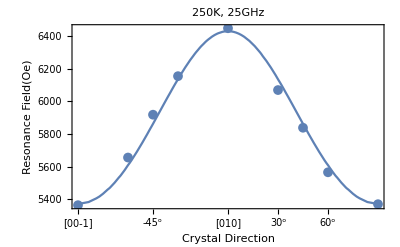

C:\Users\aoubl\Desktop\CrO2 Fit data\resonacne field fitting\Raw data-T=250K,f=25GHz.xlsx

C:\Users\aoubl\Desktop\CrO2 Fit data\resonacne field fitting\Fit data-T=250K,f=25GHz.xlsx

```mathematica
Clear["Global`*"];(*angle是沿着难轴的角度*) (*引用：Anisotropic Gilbert damping in perovskite La0.7Sr0.3MnO3 thin film*);

m1[angle_,H_,M_,U_]:=(H +M+1/4 U (3+Cos[4 angle]))*(H +U Cos[4 (angle)]);
m2[angle_,H_,M_,U_,B_]:=(H +M-U Sin[angle]^2+B/4(3-Cos[4 (angle)]))*(H -U Cos[2angle]-B Cos[4 angle]);
μ=9.27*10^-24;ℏ=1.05*10^-34;
f=25;T=250;
cc[g_]:=(2π*f*10^9/((g*μ/ℏ)))^2*10^8;

T`points={300,250,200,150,100,75,50,40,30,25,20,15,10,8,4,2};angle`points={90,60,45,30,0,-30,-45,-60,-90};
fit`data={};
Do[
data=Import["C:\\Users\\aoubl\\Desktop\\Fit data\\CrO2 data\\["<>ToString[angle]<>" degree]-all data.xlsx","EmptyField"->"Empty"];
data=data[[1]];
data=Transpose@data;
T`position=3*First@FirstPosition[T`points,T]-2;
f`data=Drop[data[[T`position]],1];f`data=f`data/10^9;R`data=Drop[data[[T`position+1]],1];
f`data=Select[f`data,#≠"Empty"&];R`data=Select[R`data,#≠"Empty"&];


f`position=First@FirstPosition[IntegerPart@f`data,f];

R`point=R`data[[f`position]];
AppendTo[fit`data,{(angle)/180*π,R`point}],{angle,angle`points}];



  data=fit`data;


{M,U,B,g}=NArgMin[{Norm[Function[{angle,H},m2[angle,H,M,U,B]-cc[g]]@@@data],{M>0,U>0,B>0,g==2}},{M,U,B,g},WorkingPrecision->10];
Print["M_eff="<>ToString[M]<>", U="<>ToString[U]<>", B="<>ToString[B]<>", g="<>ToString[g]]
fig=Show[ListPlot[data,PlotMarkers->{Automatic,10}],ContourPlot[m2[angle,H,M,U,B]==cc[g],{angle,Min[First/@data],Max[First/@data]},{H,Min[Last/@data]-500,Max[Last/@data]+500}],PlotStyle->{Green},PlotRange->All,Frame->True,ImageResolution->3000,
	FrameLabel->{"Crystal Direction","Resonance Field(Oe)"},FrameTicks->{{{0,"[010]"},{Pi/2,"[001]"},{Pi/6,30^o},{Pi/4,45^o},{π/3,60^o},{-Pi/6,-30^o},{-π/4,-45^o},{-π/3,-60^o},{-π/2,"[00-1]"}},Automatic},PlotLabel->Text[Style[Framed[ToString@T<>"K, "<>ToString[IntegerPart@f]<>"GHz"],
	Background->LightGreen,Bold]]]
data`fitted=Table[{i/π*180,H/.Flatten@NSolve[{m2[i,H,M,U,B]==cc[g],H>0},H]},{i,-π/2,π/2,π/40}];
data`raw=Table[{data[[i]][[1]]/π*180,data[[i]][[2]]},{i,Length@data}];
Export["C:\\Users\\aoubl\\Desktop\\CrO2 Fit data\\resonacne field fitting\\Raw data-T="<>ToString[T]<>"K,f="<>ToString[f]<>"GHz.xlsx",data`raw]
Export["C:\\Users\\aoubl\\Desktop\\CrO2 Fit data\\resonacne field fitting\\Fit data-T="<>ToString[T]<>"K,f="<>ToString[f]<>"GHz.xlsx",data`fitted]
```

```mathematica
T=200
```

200

{4.5,5.,5.5,6.,6.5,7.,7.5,8.,8.5,9.,9.5,10.,10.5,11.,11.5,12.,12.5,13.,13.5,14.,14.5,15.,15.5,16.,16.5,17.,17.5,20.,20.5,21.,21.5,22.,22.5,23.,23.5,24.,24.5,25.,25.5,26.5,27.,27.5,28.,28.5,29.5,30.,30.5,31.,31.5,32.,32.5,33.,33.5,36.5,37.}

InterpolatingFunction::dmval: 输入值 {7.} 位于插值函数的数据范围之外. 将使用外推法.

InterpolatingFunction::dmval: 输入值 {7.25} 位于插值函数的数据范围之外. 将使用外推法.

M_eff=8514.601761, U=851.37, B=5.01, g=2.

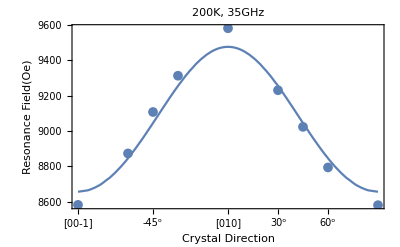

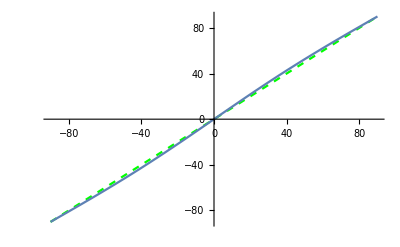

C:\Users\aoubl\Desktop\Fit data\CrO2 data\magnetic dragging\35GHz.xlsx

```mathematica
Clear["Global`*"];(*angle是沿着难轴的角度*) (*引用：Anisotropic Gilbert damping in perovskite La0.7Sr0.3MnO3 thin film*);
ClearAll[phi`m,phi`h]
(*h2=1067.660884;h4=8.012786796;*)
(*Drag Effect*)
m1[angle_,H_,M_,U_]:=(H +M+1/4 U (3+Cos[4 angle]))*(H +U Cos[4 (angle)]);
m2[angle_,H_,M_,U_,B_]:=(H +M-U Sin[angle]^2+B/4(3-Cos[4 (angle)]))*(H -U Cos[2angle]-B Cos[4 angle]);
μ=9.27*10^-24;ℏ=1.05*10^-34;
f=35;T=200;
cc[g_]:=(2π*f*10^9/((g*μ/ℏ)))^2*10^8;

T`points={300,250,200,150,100,75,50,40,30,25,20,15,10,8,4,2};angle`points={90,60,45,30,0,-30,-45,-60,-90};
fit`data={};
fre`field`data=Table[{i,fre`fun[i]},{i,7,40,0.25}];
Do[
data=Import["C:\\Users\\aoubl\\Desktop\\Fit data\\CrO2 data\\["<>ToString[angle]<>" degree]-all data.xlsx","EmptyField"->"Empty"];
data=data[[1]];
data=Transpose@data;
T`position=3*First@FirstPosition[T`points,T]-2;
f`data=Drop[data[[T`position]],1];f`data=f`data/10^9;R`data=Drop[data[[T`position+1]],1];
f`data=Select[f`data,#≠"Empty"&];R`data=Select[R`data,#≠"Empty"&];
If[angle==0,f`data`col=f`data];

f`position=First@FirstPosition[IntegerPart@f`data,f];

R`point=R`data[[f`position]];
AppendTo[fit`data,{(angle)/180*π,R`point}],{angle,angle`points}];



  data=fit`data;

{M,U,B,g}=NArgMin[{Norm[Function[{angle,H},m2[angle,H,M,U,B]-cc[g]]@@@data],{M>0,U==851.37,B==5.01,g==2}},{M,U,B,g},WorkingPrecision->10];Print["M_eff="<>ToString[M]<>", U="<>ToString[U]<>", B="<>ToString[B]<>", g="<>ToString[g]];

fig=Show[ListPlot[data,PlotMarkers->{Automatic,10}],ContourPlot[m2[angle,H,M,U,B]==cc[g],{angle,Min[First/@data],Max[First/@data]},{H,Min[Last/@data]-500,Max[Last/@data]+500}],PlotStyle->{Green},PlotRange->All,Frame->True,ImageResolution->3000,
	FrameLabel->{"Crystal Direction","Resonance Field(Oe)"},FrameTicks->{{{0,"[010]"},{Pi/2,"[001]"},{Pi/6,30^o},{Pi/4,45^o},{π/3,60^o},{-Pi/6,-30^o},{-π/4,-45^o},{-π/3,-60^o},{-π/2,"[00-1]"}},Automatic},PlotLabel->Text[Style[Framed[ToString@T<>"K, "<>ToString[IntegerPart@f]<>"GHz"],
	Background->LightGreen,Bold]]]

data=Table[{i/π*180,H/.Flatten@NSolve[{m2[i,H,M,U,B]==cc[g],H>0},H]},{i,-π/2,π/2,π/40}];



phi`H=Table[data[[i]][[1]],{i,Length@data}]/180*π;
R`point=Table[data[[i]][[2]],{i,Length@data}];
phi`M={};

Table[AppendTo[phi`M,First@Sort[phi`m/.NSolve[{R`point[[i]] Sin[phi`m-phi`H[[i]]]-U/2 Sin[2 phi`m]+B/4 Sin[4 phi`m]==0,Abs[phi`m-phi`H[[i]]]<1},phi`m,Reals],Abs[#1-phi`H[[i]]]<Abs[#2-phi`H[[i]]]&]],{i,Length@R`point}];
phi`M;
drag`data=Table[180/π*{phi`H[[i]],phi`M[[i]]},{i,Length@phi`H}];
Show[Plot[x,{x,-90,90},PlotStyle->{Dashed,Green}],ListLinePlot[drag`data,PlotRange->All,Frame->True]]
Export["C:\\Users\\aoubl\\Desktop\\Fit data\\CrO2 data\\magnetic dragging\\"<>ToString[f]<>"GHz.xlsx",drag`data]

(*AppendTo[drag`data2,{f,phi`M[[First@Flatten@Position[phi`H,π/4]]]}];*)
```

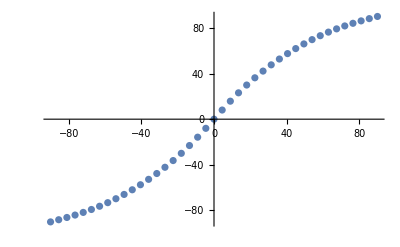

```mathematica
drag`data
```

```mathematica
phi`M[[First@Flatten@Position[phi`H,π/4]]]
```

```mathematica
0.9567248431573874*180/π
```

54.8163

```mathematica
drag`data2={};
```

```mathematica
drag`data2=Drop[drag`data2,-1]
```

{{7,1.38429},{8,1.25517},{9,1.17337},{10,1.11396},{11,1.06839},{12,1.03274},{13,1.00451},{14,0.981158},{15,0.96177},{16,0.945821},{17,0.932087}}

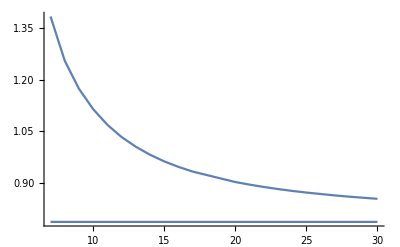

```mathematica
Show[Plot[π/4,{x,7,30}],ListLinePlot@drag`data2,PlotRange->All]
```

```mathematica
drag`data2
```

{{7,1.38429},{8,1.25517},{9,1.17337},{10,1.11396},{11,1.06839},{12,1.03274},{13,1.00451},{14,0.981158},{15,0.96177},{16,0.945821},{17,0.932087},{20,0.901621},{21,0.894071},{22,0.887274},{23,0.881169},{24,0.875721},{25,0.870931},{26,0.866736},{27,0.862594},{28,0.858955},{29,0.855794},{30,0.852686}}

```mathematica
Last@drag`data2[[First@Flatten@Position[drag`data2,20]]]
```

0.901621